### Start choosing the example:

```mathematica
t=27;
beta = 1;
A = 0.2;
V[x]
g[x]
```

0.2 Sin[2 π (1/4+x)]^2

x

```mathematica
beta
```

1

```mathematica
IntM[65]
```

-38787.6

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Intg[65]
```

-1115.41

```mathematica
Data["Entrance Vertices and Currents"]={{1,65}};
Data["Exit Vertices and Terminal Costs"]={{10,0}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.017074,Null}

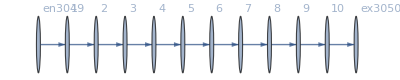

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j3051→65.,j3052→65.,j3053→65.,j3054→65.,j3055→65.,j3056→65.,j3057→65.,j3058→65.,j3059→65.,j3060→65.,j3061→65.,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65.,jt3075→65.,jt3076→0.,jt3077→65.,jt3078→0.,jt3079→65.,jt3080→0.,jt3081→65.,jt3082→0.,jt3083→65.,jt3084→0.,jt3085→65.,jt3086→0.,jt3087→65.,jt3088→0.,jt3089→65.,jt3090→0.,jt3091→65.,jt3092→0.,u3093→585.,u3094→520.,u3095→455.,u3096→390.,u3097→325.,u3098→260.,u3099→195.,u3100→130.,u3101→65.,u3102→0.,u3103→585.,u3104→-65.+1. 585.,u3105→-65.+1. 520.,u3106→-65.+1. 455.,u3107→-65.+1. 390.,u3108→-65.+1. 325.,u3109→-65.+1. 260.,u3110→-65.+1. 195.,u3111→-65.+1. 130.,u3112→-65.+1. 65.,u3113→0.,u3114→0.+1. 585.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 0.

FRX1: The relative Error on the nonlinear terms is 0.

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→45.4737,u3094→40.4211,u3095→35.3685,u3096→30.3158,u3097→25.2632,u3098→20.2105,u3099→15.1579,u3100→10.1053,u3101→5.05264,u3102→0.,u3103→0.+1. 45.4737,u3104→40.4211,u3105→35.3685,u3106→30.3158,u3107→25.2632,u3108→20.2105,u3109→15.1579,u3110→10.1053,u3111→5.05264,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 45.4737)|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 9.03649×10^-17

FRX1: The relative Error on the nonlinear terms is 9.03649×10^-17

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→54.245,u3094→48.2177,u3095→42.1905,u3096→36.1633,u3097→30.1361,u3098→24.1089,u3099→18.0817,u3100→12.0544,u3101→6.02722,u3102→0.,u3103→0.+1. 54.245,u3104→48.2177,u3105→42.1905,u3106→36.1633,u3107→30.1361,u3108→24.1089,u3109→18.0817,u3110→12.0544,u3111→6.02722,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 54.245)|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 2.2172×10^-16

FRX1: The relative Error on the nonlinear terms is 2.2172×10^-16

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→80.262,u3094→71.344,u3095→62.426,u3096→53.508,u3097→44.59,u3098→35.672,u3099→26.754,u3100→17.836,u3101→8.918,u3102→0.,u3103→0.+1. 80.262,u3104→71.344,u3105→62.426,u3106→53.508,u3107→44.59,u3108→35.672,u3109→26.754,u3110→17.836,u3111→8.918,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 80.262)|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 0.

FRX1: The relative Error on the nonlinear terms is 0.

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→406.236,u3094→361.099,u3095→315.961,u3096→270.824,u3097→225.687,u3098→180.549,u3099→135.412,u3100→90.2746,u3101→45.1373,u3102→0.,u3103→0.+1. 406.236,u3104→361.099,u3105→315.961,u3106→270.824,u3107→225.687,u3108→180.549,u3109→135.412,u3110→90.2746,u3111→45.1373,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 406.236)|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The relative Error on the nonlinear terms is ∞

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→585.,u3094→520.,u3095→455.,u3096→390.,u3097→325.,u3098→260.,u3099→195.,u3100→130.,u3101→65.,u3102→0.,u3103→0.+1. 585.,u3104→520.,u3105→455.,u3106→390.,u3107→325.,u3108→260.,u3109→195.,u3110→130.,u3111→65.,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 585.)|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.62976×10^-15

FRX1: The relative Error on the nonlinear terms is 1.62976×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→1369.77,u3094→1217.57,u3095→1065.37,u3096→913.177,u3097→760.981,u3098→608.785,u3099→456.589,u3100→304.392,u3101→152.196,u3102→0.,u3103→0.+1. 1369.77,u3104→1217.57,u3105→1065.37,u3106→913.177,u3107→760.981,u3108→608.785,u3109→456.589,u3110→304.392,u3111→152.196,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 1369.77)|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.57114×10^-15

FRX1: The relative Error on the nonlinear terms is 1.57114×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→7507.74,u3094→6673.55,u3095→5839.36,u3096→5005.16,u3097→4170.97,u3098→3336.77,u3099→2502.58,u3100→1668.39,u3101→834.194,u3102→0.,u3103→0.+1. 7507.74,u3104→6673.55,u3105→5839.36,u3106→5005.16,u3107→4170.97,u3108→3336.77,u3109→2502.58,u3110→1668.39,u3111→834.194,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 7507.74)|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.45215×10^-15

FRX1: The relative Error on the nonlinear terms is 1.45215×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→15564.9,u3094→13835.5,u3095→12106.1,u3096→10376.6,u3097→8647.18,u3098→6917.75,u3099→5188.31,u3100→3458.87,u3101→1729.44,u3102→0.,u3103→0.+1. 15564.9,u3104→13835.5,u3105→12106.1,u3106→10376.6,u3107→8647.18,u3108→6917.75,u3109→5188.31,u3110→3458.87,u3111→1729.44,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 15564.9)|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.85655×10^-15

FRX1: The relative Error on the nonlinear terms is 1.85655×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→15577.1,u3094→13846.3,u3095→12115.5,u3096→10384.7,u3097→8653.94,u3098→6923.15,u3099→5192.37,u3100→3461.58,u3101→1730.79,u3102→0.,u3103→0.+1. 15577.1,u3104→13846.3,u3105→12115.5,u3106→10384.7,u3107→8653.94,u3108→6923.15,u3109→5192.37,u3110→3461.58,u3111→1730.79,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 15577.1)|>

```mathematica
alpha = 1.605;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.39424×10^-15

FRX1: The relative Error on the nonlinear terms is 1.39424×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→16187.2,u3094→14388.6,u3095→12590.,u3096→10791.4,u3097→8992.87,u3098→7194.29,u3099→5395.72,u3100→3597.15,u3101→1798.57,u3102→0.,u3103→0.+1. 16187.2,u3104→14388.6,u3105→12590.,u3106→10791.4,u3107→8992.87,u3108→7194.29,u3109→5395.72,u3110→3597.15,u3111→1798.57,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 16187.2)|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.03819×10^-15

FRX1: The relative Error on the nonlinear terms is 1.03819×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→16839.,u3094→14968.,u3095→13097.,u3096→11226.,u3097→9355.01,u3098→7484.01,u3099→5613.,u3100→3742.,u3101→1871.,u3102→0.,u3103→0.+1. 16839.,u3104→14968.,u3105→13097.,u3106→11226.,u3107→9355.01,u3108→7484.01,u3109→5613.,u3110→3742.,u3111→1871.,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 16839.)|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 9.55905×10^-16

FRX1: The relative Error on the nonlinear terms is 9.55905×10^-16

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→18238.2,u3094→16211.7,u3095→14185.2,u3096→12158.8,u3097→10132.3,u3098→8105.85,u3099→6079.39,u3100→4052.93,u3101→2026.46,u3102→0.,u3103→0.+1. 18238.2,u3104→16211.7,u3105→14185.2,u3106→12158.8,u3107→10132.3,u3108→8105.85,u3109→6079.39,u3110→4052.93,u3111→2026.46,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 18238.2)|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 0.

FRX1: The relative Error on the nonlinear terms is 0.

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→23337.6,u3094→20744.5,u3095→18151.5,u3096→15558.4,u3097→12965.3,u3098→10372.3,u3099→7779.2,u3100→5186.13,u3101→2593.07,u3102→0.,u3103→0.+1. 23337.6,u3104→20744.5,u3105→18151.5,u3106→15558.4,u3107→12965.3,u3108→10372.3,u3109→7779.2,u3110→5186.13,u3111→2593.07,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 23337.6)|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.22504×10^-15

FRX1: The relative Error on the nonlinear terms is 1.22504×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→36099.1,u3094→32088.,u3095→28077.,u3096→24066.,u3097→20055.,u3098→16044.,u3099→12033.,u3100→8022.01,u3101→4011.01,u3102→0.,u3103→0.+1. 36099.1,u3104→32088.,u3105→28077.,u3106→24066.,u3107→20055.,u3108→16044.,u3109→12033.,u3110→8022.01,u3111→4011.01,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 36099.1)|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.41006×10^-15

FRX1: The relative Error on the nonlinear terms is 1.41006×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→96324.4,u3094→85621.6,u3095→74918.9,u3096→64216.2,u3097→53513.5,u3098→42810.8,u3099→32108.1,u3100→21405.4,u3101→10702.7,u3102→0.,u3103→0.+1. 96324.4,u3104→85621.6,u3105→74918.9,u3106→64216.2,u3107→53513.5,u3108→42810.8,u3109→32108.1,u3110→21405.4,u3111→10702.7,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 96324.4)|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.47946×10^-15

FRX1: The relative Error on the nonlinear terms is 1.47946×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→307240.,u3094→273102.,u3095→238964.,u3096→204827.,u3097→170689.,u3098→136551.,u3099→102413.,u3100→68275.6,u3101→34137.8,u3102→0.,u3103→0.+1. 307240.,u3104→273102.,u3105→238964.,u3106→204827.,u3107→170689.,u3108→136551.,u3109→102413.,u3110→68275.6,u3111→34137.8,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 307240.)|>

```mathematica
alpha = 1.91;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The relative Error on the nonlinear terms is 1.51489×10^-15

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The relative Error on the nonlinear terms is 1.51489×10^-15

<|j3051→65,j3052→65,j3053→65,j3054→65,j3055→65,j3056→65,j3057→65,j3058→65,j3059→65,j3060→65,j3061→65,j3062→0.,j3063→0.,j3064→0.,j3065→0.,j3066→0.,j3067→0.,j3068→0.,j3069→0.,j3070→0.,j3071→0.,j3072→0.,jt3073→0.,jt3074→65,jt3075→65,jt3076→0.,jt3077→65,jt3078→0.,jt3079→65,jt3080→0.,jt3081→65,jt3082→0.,jt3083→65,jt3084→0.,jt3085→65,jt3086→0.,jt3087→65,jt3088→0.,jt3089→65,jt3090→0.,jt3091→65,jt3092→0.,u3093→349089.,u3094→310301.,u3095→271513.,u3096→232726.,u3097→193938.,u3098→155151.,u3099→116363.,u3100→77575.3,u3101→38787.6,u3102→0.,u3103→0.+1. 349089.,u3104→310301.,u3105→271513.,u3106→232726.,u3107→193938.,u3108→155151.,u3109→116363.,u3110→77575.3,u3111→38787.6,u3112→0,u3113→0.,u3114→0.+1. (0.+1. 349089.)|>

```mathematica
aux = <|j2603->65,u2655->0.,j2593->65,j2594->65,j2595->65,j2596->65,j2597->65,j2598->65,j2599->65,j2600->65,j2601->65,j2602->65,j2604->0.,j2605->0.,j2606->0.,j2607->0.,j2608->0.,j2609->0.,j2610->0.,j2611->0.,j2612->0.,j2613->0.,j2614->0.,jt2615->0.,jt2616->65,jt2617->65,jt2618->0.,jt2619->65,jt2620->0.,jt2621->65,jt2622->0.,jt2623->65,jt2624->0.,jt2625->65,jt2626->0.,jt2627->65,jt2628->0.,jt2629->65,jt2630->0.,jt2631->65,jt2632->0.,jt2633->65,jt2634->0.,u2644->0.,u2656->0.+1. (0.+1. 7.153383732831773*^19),u2645->0.+1. 7.153383732831773*^19,u2646->6.358563318072687*^19,u2647->5.5637429033136005*^19,u2648->4.768922488554515*^19,u2649->3.974102073795428*^19,u2650->3.1792816590363427*^19,u2651->2.384461244277257*^19,u2652->1.5896408295181713*^19,u2653->7.948204147590857*^18,u2654->0,u2635->7.153383732831773*^19,u2636->6.358563318072687*^19,u2637->5.5637429033136005*^19,u2638->4.768922488554515*^19,u2639->3.974102073795428*^19,u2640->3.1792816590363427*^19,u2641->2.384461244277257*^19,u2642->1.5896408295181713*^19,u2643->7.948204147590857*^18|>;
```

```mathematica
MFGEquations["Nlhs"]/MFGEquations["Nrhs"]
MFGEquations["Nlhs"]/.aux

MFGEquations["Nrhs"]/.aux
(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nrhs"]/.aux
```

{(j3051-j3062-u3093+u3104)/(j3051-j3062+IntM[j3051-j3062]),(j3052-j3063-u3094+u3105)/(j3052-j3063+IntM[j3052-j3063]),(j3053-j3064-u3095+u3106)/(j3053-j3064+IntM[j3053-j3064]),(j3054-j3065-u3096+u3107)/(j3054-j3065+IntM[j3054-j3065]),(j3055-j3066-u3097+u3108)/(j3055-j3066+IntM[j3055-j3066]),(j3056-j3067-u3098+u3109)/(j3056-j3067+IntM[j3056-j3067]),(j3057-j3068-u3099+u3110)/(j3057-j3068+IntM[j3057-j3068]),(j3058-j3069-u3100+u3111)/(j3058-j3069+IntM[j3058-j3069]),(j3059-j3070-u3101+u3112)/(j3059-j3070+IntM[j3059-j3070])}

{j3051-j3062-u3093+u3104,j3052-j3063-u3094+u3105,j3053-j3064-u3095+u3106,j3054-j3065-u3096+u3107,j3055-j3066-u3097+u3108,j3056-j3067-u3098+u3109,j3057-j3068-u3099+u3110,j3058-j3069-u3100+u3111,j3059-j3070-u3101+u3112}

{j3051-j3062+IntM[j3051-j3062],j3052-j3063+IntM[j3052-j3063],j3053-j3064+IntM[j3053-j3064],j3054-j3065+IntM[j3054-j3065],j3055-j3066+IntM[j3055-j3066],j3056-j3067+IntM[j3056-j3067],j3057-j3068+IntM[j3057-j3068],j3058-j3069+IntM[j3058-j3069],j3059-j3070+IntM[j3059-j3070]}

{(-u3093+u3104-IntM[j3051-j3062])/(j3051-j3062+IntM[j3051-j3062]),(-u3094+u3105-IntM[j3052-j3063])/(j3052-j3063+IntM[j3052-j3063]),(-u3095+u3106-IntM[j3053-j3064])/(j3053-j3064+IntM[j3053-j3064]),(-u3096+u3107-IntM[j3054-j3065])/(j3054-j3065+IntM[j3054-j3065]),(-u3097+u3108-IntM[j3055-j3066])/(j3055-j3066+IntM[j3055-j3066]),(-u3098+u3109-IntM[j3056-j3067])/(j3056-j3067+IntM[j3056-j3067]),(-u3099+u3110-IntM[j3057-j3068])/(j3057-j3068+IntM[j3057-j3068]),(-u3100+u3111-IntM[j3058-j3069])/(j3058-j3069+IntM[j3058-j3069]),(-u3101+u3112-IntM[j3059-j3070])/(j3059-j3070+IntM[j3059-j3070])}

### What we this plot for?

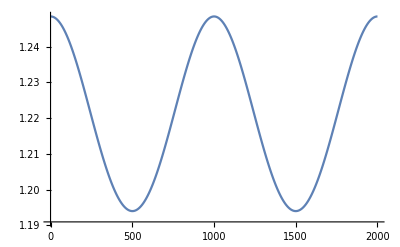

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.